# Lab 11: Complex Analysis -- Carter Colton

```mathematica
Clear["`*" ]
```

## Assignment 1: Graphical Interpretation of Re, Im, Abs, Arg, and Conjugate

(a) What are Re[z] and Im[z] for this particular point z_0, and what do they represent on the above graph?
(b) What are Abs[z] and Arg[z] for this particular point z_0, and what do they represent on the above graph? 
(c) Make a similar combination point & arrow plot for Conjugate[z0]. What does the complex conjugate represent, graphically?

```mathematica
complexToXY[z_] := {Re[z],Im[z]} ;
complexToXY[2+3I]  (* testing *)

XYToComplex[{x_,y_}] :=x + I y
XYToComplex[{2,3}]
```

{2,3}

2+3 ⅈ

3+4 ⅈ

{3,4}

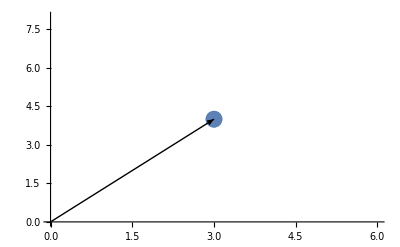

```mathematica
z0 = 3+4 I
z0coords = z0 // complexToXY
plot1=ListPlot[{z0coords},PlotStyle->PointSize[0.03]];
plot2 = Graphics[Arrow[{{0,0},z0coords}] ];
Show[plot1,plot2]
```

```mathematica
Re[z0]
Im[z0]
```

3

4

The Re part of the graph represents the x-component of the resulting vector and the Im part of the graph represents the y-component of the resulting vector

```mathematica
Abs[z0]
Arg[z0]
```

5

ArcTan[4/3]

The Abs part of the graph represents the magnitude of the resulting vector and the Arg represents the angle that is made with the x-axis and the resulting vector

3-4 ⅈ

{3,-4}

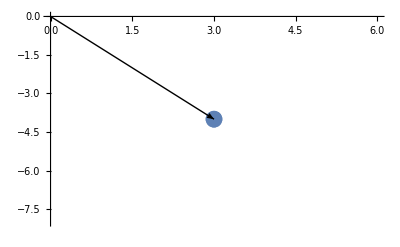

```mathematica
z0 = 3+4 I;
z0con=Conjugate[z0]
z0coordscon = z0con // complexToXY
plot1=ListPlot[{z0coordscon},PlotStyle->PointSize[0.03]];
plot2 = Graphics[Arrow[{{0,0},z0coordscon}] ];
Show[plot1,plot2]
```

The complex conjugate represents the reflection of z0 over the y-axis. It also represents a rotation or a phase shift.

## Assignment 2: Random Complex Numbers and Interpretation of Sign

(a) Use RandomComplex to generate 100 random complex numbers within the rectangle defined by corners at -1-i  and 1+i .  Convert them to {x, y} points (the Map function,  /@ , may be helpful) and ListPlot them using AspectRatio → 1. 
(b) Now apply the Sign function to your list of complex numbers and plot again. Use your plot to figure out the graphical interpretation of the Sign function.

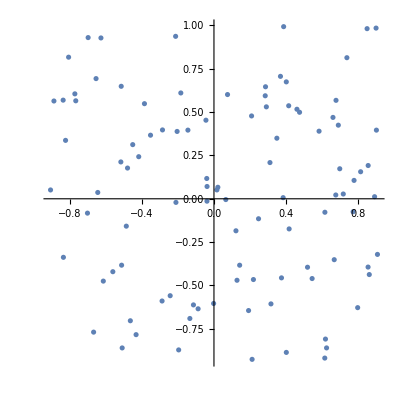

```mathematica
ListPlot[complexToXY/@Table[RandomComplex[{-1-I,1+I}],{n,1,100}], AspectRatio->1]
```

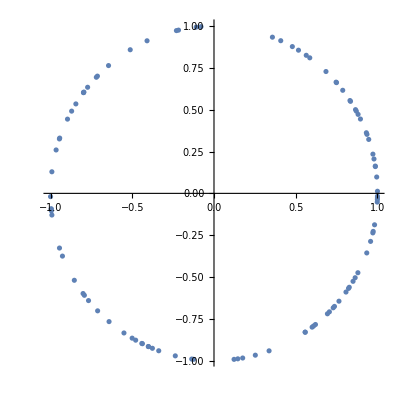

```mathematica
ListPlot[complexToXY/@Sign[Table[RandomComplex[{-1-I,1+I}],{n,1,100}]], AspectRatio->1]
```

The Sign function normalizes the complex numbers, thus projecting them into a unit circle

## Assignment 3: Exponential and Sin/Cos Formulas

(a) Use ExpToTrig to convert e^ix into trigonometric form, to verify that Mathematica “knows” Euler’s formula.
(b) Use ExpToTrig to convert e^x into trigonometric form. This is the analog of Euler’s formula for hyperbolic functions sinh(x) and cosh(x).
(c) Use TrigToExp to convert cos(x) and sin(x) into exponential form.
(d) Use TrigToExp to convert cosh(x) and sinh(x) into exponential form. Compare to the exponential forms of cosine and sine.
(e) All six of these results are used so frequently in physics classes that they are worth memorizing, in case you don’t already know them.  (Note: the result for sin(x) is usually written with the “i” in the denominator, using 1/i = -i.)

```mathematica
ExpToTrig[E^(I*x)]
```

Cos[x]+ⅈ Sin[x]

```mathematica
ExpToTrig[E^x]
```

Cosh[x]+Sinh[x]

```mathematica
TrigToExp[Cos[x]]
TrigToExp[Sin[x]]
```

ⅇ^(-ⅈ x)/2+ⅇ^(ⅈ x)/2

1/2 ⅈ ⅇ^(-ⅈ x)-1/2 ⅈ ⅇ^(ⅈ x)

```mathematica
TrigToExp[Cosh[x]]
TrigToExp[Sinh[x]]
```

ⅇ^-x/2+ⅇ^x/2

-ⅇ^-x/2+ⅇ^x/2

## Assignment 4: A “Rotate by Angle” Function

Create a function, rotate[number_, angle_], which “rotates” a complex number by multiplying it by a unit vector having the desired angle. Test out your function by rotating the vector z_1=2+i  by 35 degrees and plotting the results (initial vector and rotated vector) with the complexToXY function and commands modified from the “Complex numbers as vectors” section above. Use PlotRange→ {{-2,2},{-2,2}}  and  AspectRatio→1 as options in your Graphics command so that the rotation looks right.

```mathematica
rotatebyangle[number_,angle_]:=Module[{newnumber},
newnumber=E^(I*angle)*number;
newnumber
]
```

```mathematica
z1=2+I;
```

```mathematica
z1new=rotatebyangle[z1,35Degree]
```

(2+ⅈ) ⅇ^(35 ⅈ °)

```mathematica
objects={Arrow[{{0,0},complexToXY[z1]}],Arrow[{{0,0},complexToXY[z1new]}]}
```

{Arrow[{{0,0},{2,1}}],Arrow[{{0,0},{2 Cos[35 °]-Sin[35 °],Cos[35 °]+2 Sin[35 °]}}]}

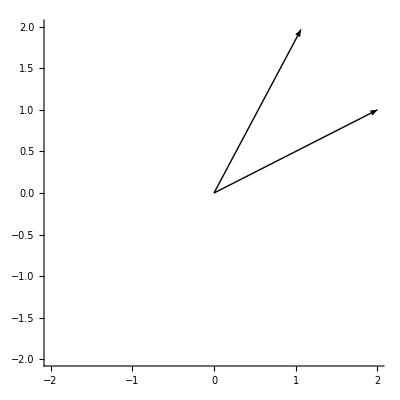

```mathematica
Graphics[objects,PlotRange->{{-2,2},{-2,2}}, AspectRatio->1,Axes->True]
```

## Assignment 5: Fresnel Coefficients

(a) According to this website database, for 532 nm light (green), aluminum has an index of refraction of 0.939 + 6.42i. If you are shining a green laser pointer (532 nm, 1 mW of power) at an aluminum mirror, how much laser power will reflect? The answer will depend on the incident angle θ_i, so use Mathematica to make a plot of the reflected power as a function of θ_i (in radians). Note that the reflecting power is described by R, not r; the two are related to each other by R=|r|^2. Plot the reflected powers for both s and p polarizations on the same graph as I’ve done in the graph above. Hint: Since the equations are given in terms of θ_i and θ_t, you’ll have to use Snell’s law to relate θ_t to the incident angle θ_i:  n_1 sinθ_i= n_2 sinθ_t,  or θ_t=sin^-1(n_1 sinθ_i/n_2). The complex index will give you a complex θ_t, but don’t worry about that--the equations still hold for a complex angle of transmission even if a complex angle can’t be visualized. Mathematica can take sines, cosines, and tangents of complex angles just fine.
(b) Find the angle that corresponds to the minimum value of the p-polarization graph, and how much p-polarized light will still reflect at that “Brewster’s angle”.

```mathematica
n1=1;
n2=0.939+6.42*I;
thetat=ArcSin[n1*Sin[thetai]/n2];
```

```mathematica
Rs=(n1*Cos[thetai]-n2*Cos[thetat])/(n1*Cos[thetai]+n2*Cos[thetat])*Conjugate[(n1*Cos[thetai]-n2*Cos[thetat])/(n1*Cos[thetai]+n2*Cos[thetat])]
```

((Conjugate[Cos[thetai]]-(0.939-6.42 ⅈ) Conjugate[√(1+(0.022759+0.00680307 ⅈ) Sin[thetai]^2)]) (Cos[thetai]-(0.939+6.42 ⅈ) √(1+(0.022759+0.00680307 ⅈ) Sin[thetai]^2)))/((Conjugate[Cos[thetai]]+(0.939-6.42 ⅈ) Conjugate[√(1+(0.022759+0.00680307 ⅈ) Sin[thetai]^2)]) (Cos[thetai]+(0.939+6.42 ⅈ) √(1+(0.022759+0.00680307 ⅈ) Sin[thetai]^2)))

```mathematica
Rp=(n1*Cos[thetat]-n2*Cos[thetai])/(n1*Cos[thetat]+n2*Cos[thetai])*Conjugate[(n1*Cos[thetat]-n2*Cos[thetai])/(n1*Cos[thetat]+n2*Cos[thetai])]
```

(((-0.939+6.42 ⅈ) Conjugate[Cos[thetai]]+Conjugate[√(1+(0.022759+0.00680307 ⅈ) Sin[thetai]^2)]) ((-0.939-6.42 ⅈ) Cos[thetai]+√(1+(0.022759+0.00680307 ⅈ) Sin[thetai]^2)))/(((0.939-6.42 ⅈ) Conjugate[Cos[thetai]]+Conjugate[√(1+(0.022759+0.00680307 ⅈ) Sin[thetai]^2)]) ((0.939+6.42 ⅈ) Cos[thetai]+√(1+(0.022759+0.00680307 ⅈ) Sin[thetai]^2)))

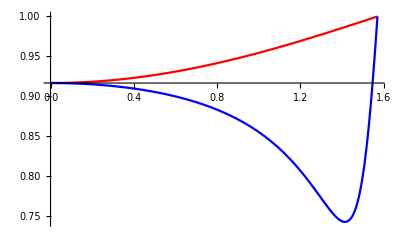

```mathematica
plot1=Plot[Rs,{thetai,0,Pi/2},PlotStyle->Red];
plot2=Plot[Rp,{thetai,0,Pi/2},PlotStyle->Blue];
Show[plot1,plot2,PlotRange->All]
```

```mathematica
FindMinimum[Rp,thetai, Method->"PrincipalAxis"]
```

{0.742261,{thetai→1.4145}}

```mathematica
thetai/.%[[2]]
```

1.4145

```mathematica
%/Degree
```

81.0448

## Assignment 6: Plotting e^x as a Complex Function

What does it mean to plot a complex function? The seemingly simple matter of plotting a function is made more “complex” (ha ha) in two different ways: 

• Since the function can take a complex value as an input, you technically need to have the whole complex plane as the domain of the function. There are two typical ways of dealing with this: (1) do a Plot3D as a function of x and y, where x and y are the real and imaginary parts of the complex number input, or (2) restrict your range to a linear subset of the complex plane, such as only the real numbers, or only the purely imaginary numbers, or only the numbers that have equal real and imaginary components, and do a regular plot with that linear subset as the “x-axis”.

• Since the function can return a complex value as an output, you need to have the ability to plot two independent numbers as the output. The typical way to deal with this is to plot the real and imaginary parts of the output, separately.

Now for the assignment:

(a) Plot the real and imaginary components of f(x) =e^x on two separate graphs, using the real numbers from -2 to 2 as the x-axis. (I basically did this above.)
(b) Plot the real and imaginary components of f(x) =e^x on two separate graphs, using the purely imaginary numbers from -2i to 2i as the x-axis.  Be careful in how you do this as you cannot use complex numbers as the limits for the plot variable. So, for example, you cannot simply do this: Plot[Re[Exp[x]],{x,-2 I,2 I}]
(c) Plot the real and imaginary components of f(x) =e^x on two separate graphs, using the numbers that have equal real and imaginary components from -2-2i to 2+2i as the x-axis. See the “Be careful” comment of part (b).
(d) Plot the real and imaginary components of f(x) =e^x on two separate graphs, using Plot3D to incorporate the entire complex plane as the domain, i.e. a square that incorporates the previous three linear subset domains. Show that the results of (a), (b), and (c) are visible in the two plots.
(e) Use the ComplexExpand command to separate the real and imaginary parts of e^(x+iy). From the results, you can explicitly see the two separate functions that make up our complex function f(x)=e^x. How does the output of ComplexExpand relate to your plots?

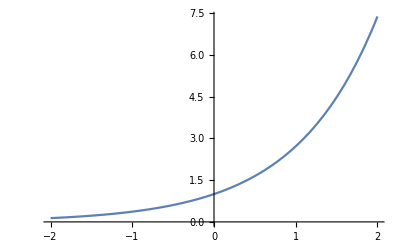

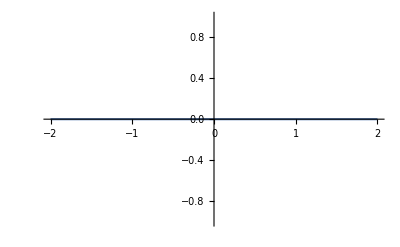

```mathematica
Plot[Re[Exp[x]],{x,-2,2}]
Plot[Im[Exp[x]],{x,-2,2}]
```

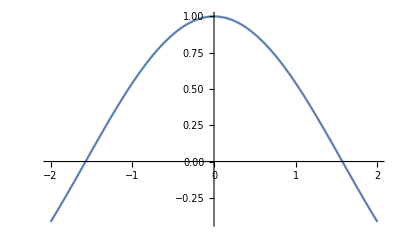

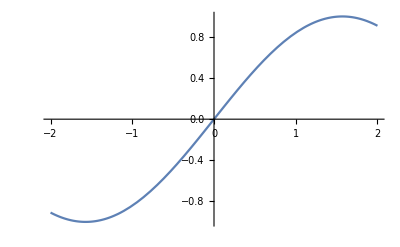

```mathematica
Plot[Re[Exp[I*x]],{x,-2,2}]
Plot[Im[Exp[I*x]],{x,-2,2}]
```

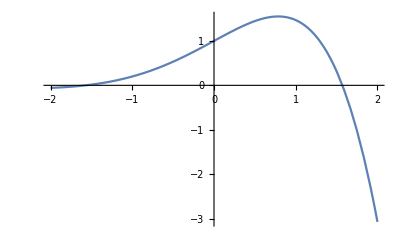

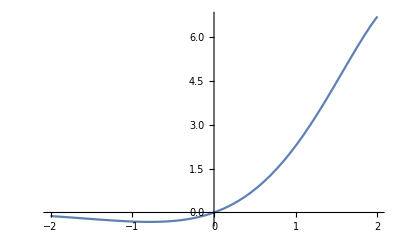

```mathematica
Plot[Re[Exp[x+I*x]],{x,-2,2}]
Plot[Im[Exp[x+I*x]],{x,-2,2}]
```

```mathematica
Plot3D[Re[Exp[x+I*y]],{x,-2,2},{y,-2,2},PlotRange->All]
Plot3D[Im[Exp[x+I*y]],{x,-2,2},{y,-2,2},PlotRange->All]
```

-Graphics3D-

-Graphics3D-

```mathematica
ComplexExpand[E^(x+I*y)]
```

ⅇ^x Cos[y]+ⅈ ⅇ^x Sin[y]

The first term of this answer is the real part of e^x, which corresponds to my first plot. The second term is the imaginary part, which corresponds to my second plot. The third plot is represented as the combination of the real and the imaginary plots.

## Assignment 7: Laurent Series and Residue of 1/(1-e^(z-0.5))

(a)  Plot the real and imaginary parts of this function:  f=1/(1-e^(z-0.5)). Feel free to copy & paste the code just above as a starting point. Where is the pole, z_0?
(b) Compute the 10^th-order Laurent series expansion around that pole, i.e. the series expansion of f in powers of (z-z_0).
(c) Now use Mathematica’s built-in SeriesCoefficient function to determine the a_-1 and a_9 coefficients of the series expansion of f in powers of (z-z_0) and verify that they match what you found from part (a). If you just care about one or two of the coefficients, this is a more efficient method than using Series.
(d) The a_-1 coefficient of a Laurent series expansion has some special significance as we’ll see below, so there’s a special command just for it: Residue. Verify that the Residue command gives the same result as SeriesCoefficient for the a_-1 term in the series.

```mathematica
Clear[z,z0]
```

```mathematica
f=1/(1-E^(z-0.5));
list={Re[f],Im[f]}   /. z-> x+I y;
Plot3D[# , {x,-2 , 2 },{y,-2 ,2 },AxesLabel->{"x","y",None},PlotRange->{-30,30}, PlotLabel->#]&  /@ list
```

{-Graphics3D-,-Graphics3D-}

The pole occurs at z=0.5

```mathematica
Series[f,{z,0.5,10}] //Normal  (* doesn't contain any negative powers of (z-i) *)
f /. z->I //N
```

1/2+1/12 (0.5-z)-1/(-0.5+z)+1/720 (-0.5+z)^3-(-0.5+z)^5/30240+(-0.5+z)^7/1209600-(-0.5+z)^9/47900160

0.943619+0.716361 ⅈ

```mathematica
SeriesCoefficient[f,{z,0.5,-1}]//N
SeriesCoefficient[f,{z,0.5,9}]//N
```

-1.

-2.08768×10^-8

```mathematica
Residue[f,{z,0.5}]
```

-1.

## Assignment 8: A Much More Interesting Path

Still using  f(x,y)=x^2+y^2, consider yet another path going from (0,0,0) to (1,1,2): 

Path 3:  x = sqrt(t);  y = sin(t 5π/2);  t goes from 0 to 1 

(a) Make a plot of the path represented by that parametrization
(b) Make a plot of the area represented by the the integral of f  along this path. To verify that this plot is correct, also Show it together with the above plot1. It should intersect the function in plot 1 everywhere along the path.
(c) Use my “pathintegral” function to calculate the area represented by your plot.

```mathematica
Clear[f,x,y]
```

```mathematica
f = x ^2 + y^2;
plot1 = Plot3D[f,{x,-1.5,1.5},{y,-1.5,1.5} ,BoxRatios->{1,1,1}];
plot2= ListPointPlot3D[{{ 0,0,0},{1,1,2}}, PlotStyle->PointSize[.05], BoxRatios->{1,1,1}];
Show[plot1,plot2]
```

-Graphics3D-

```mathematica
plot0=ParametricPlot3D[{x,y,f} /.{ x -> Sqrt[t], y-> Sin[t*5*Pi/2]},{t,0,1}, BoxRatios->{1,1,1}];
plot00=ParametricPlot3D[{x,y,0} /.{ x -> Sqrt[t], y-> Sin[t*5*Pi/2]},{t,0,1}, BoxRatios->{1,1,1}, PlotStyle->Dashed]; (* projection in the x-y plane *)
Show[plot0,plot00, PlotRange->All]
```

-Graphics3D-

```mathematica
plot0area=ParametricPlot3D[{x,y,z}  /.{ x ->  Sqrt[t], y-> Sin[t*5*Pi/2]},{t,0,1},{z,0,f /.{ x ->  Sqrt[t], y-> Sin[t*5*Pi/2]}}, BoxRatios->{1,1,1},PlotRange->All,PlotPoints->50]
Show[plot0,plot0area]
```

-Graphics3D-

-Graphics3D-

```mathematica
pathintegral[f_,xoft_,yoft_,t_,tstart_,tend_] :=  Module[{extrafactor,foft},   
	(*  f = f(x,y);  
		xoft = x as func of t for the particular path, 
		yoft = y as func of t for the particular path,  
		t is just the letter t, 
		tstart and tend are limits of t  *)
extrafactor=Sqrt[D[xoft,t]^2 + D[yoft,t]^2];
foft = f /. {x->xoft, y-> yoft} ;
NIntegrate[foft * extrafactor,{t,tstart,tend}]
]
```

```mathematica
pathintegral[x^2 + y^2, Sqrt[t],Sin[t*5*Pi/2],t,0,1] //N
```

4.27486

## Assignment 9: Residue Theorem Demonstration

```mathematica
Clear["`*" ]
```

(a) Determine the residues for the function g at each of the three poles. Recall the residue is the coefficient of the (z-z_0)^-1 term of the series expansion. You can do this via a Series expansion, via the SeriesCoefficient function, or via the Residue command. Or all three, if you wish. Record (on a piece of paper) the residue of each pole.

(b) Here’s some code which defines and displays a parametric path for the integral, then integrates it. You can specify the details of the circular path by adjusting z0 and r in the first line. (It should currently be set to integrate around a circle containing just the middle pole.) Perform three integrals, one around each pole, and verify that the result of each integral is 2πi  times the residue at that pole.

(c) Test out the residue theorem by defining your path to include no poles. The function should integrate to zero.

(d)  Finally, change z_0 back to 0 and make r large enough to include all three poles.  Verify that this larger path integral yields the 2πi  times the sum of all three residues.

```mathematica
g[z_] = 3/(z+z^3)
gplot=Plot3D[Abs[g[x+I y]],{x,-3,3},{y,-3,3},AxesLabel->{"x","y",None},Axes->{True,True,False},MeshStyle->Gray,PlotPoints->20,PlotRange->{0,10},LabelStyle->Medium,ViewPoint->{0,0,20},SphericalRegion->True]
```

3/(z+z^3)

-Graphics3D-

```mathematica
Solve[z+z^3==0]
```

{{z→0},{z→-ⅈ},{z→ⅈ}}

```mathematica
Residue[g[z],{z,0}]
Residue[g[z],{z,-I}]
Residue[g[z],{z,I}]
```

3

-3/2

-3/2

```mathematica
z0 = 0;  r= 1/2;  (* z0 is the expansion point, r is the integration-path radius *)
parametricpath[th_] := {r*Cos[th]+Re[z0],r*Sin[th]+Im[z0], Abs[g[r*(Cos[th]+I Sin[th])+z0]]}
Show[ gplot,
Plot3D[Abs[g[x+I y]],{x,-3,3},{y,-3,3},AxesLabel->{"x","y",None},Axes->{True,True,False},MeshStyle->Gray,PlotPoints->20,PlotRange->{0,10},LabelStyle->Medium,ViewPoint->{0,0,20},SphericalRegion->True],
ParametricPlot3D[parametricpath[th],{th,0,2Pi},PlotStyle->{Thickness[0.01],Black}]
]
zzz= z0 +  r*Exp[I θ];
integrand = g[zzz] D[zzz,θ];
Integrate[integrand ,{θ,0,2Pi}]
```

-Graphics3D-

6 ⅈ π

```mathematica
z0 = -I;  r= 1/2;  (* z0 is the expansion point, r is the integration-path radius *)
parametricpath[th_] := {r*Cos[th]+Re[z0],r*Sin[th]+Im[z0], Abs[g[r*(Cos[th]+I Sin[th])+z0]]}
Show[ gplot,
Plot3D[Abs[g[x+I y]],{x,-3,3},{y,-3,3},AxesLabel->{"x","y",None},Axes->{True,True,False},MeshStyle->Gray,PlotPoints->20,PlotRange->{0,10},LabelStyle->Medium,ViewPoint->{0,0,20},SphericalRegion->True],
ParametricPlot3D[parametricpath[th],{th,0,2Pi},PlotStyle->{Thickness[0.01],Black}]
]
zzz= z0 +  r*Exp[I θ];
integrand = g[zzz] D[zzz,θ];
Integrate[integrand ,{θ,0,2Pi}]
```

-Graphics3D-

-3 ⅈ π

```mathematica
z0 = I;  r= 1/2;  (* z0 is the expansion point, r is the integration-path radius *)
parametricpath[th_] := {r*Cos[th]+Re[z0],r*Sin[th]+Im[z0], Abs[g[r*(Cos[th]+I Sin[th])+z0]]}
Show[ gplot,
Plot3D[Abs[g[x+I y]],{x,-3,3},{y,-3,3},AxesLabel->{"x","y",None},Axes->{True,True,False},MeshStyle->Gray,PlotPoints->20,PlotRange->{0,10},LabelStyle->Medium,ViewPoint->{0,0,20},SphericalRegion->True],
ParametricPlot3D[parametricpath[th],{th,0,2Pi},PlotStyle->{Thickness[0.01],Black}]
]
zzz= z0 +  r*Exp[I θ];
integrand = g[zzz] D[zzz,θ];
Integrate[integrand ,{θ,0,2Pi}]
```

-Graphics3D-

-3 ⅈ π

```mathematica
z0 = 1;  r= 1/2;  (* z0 is the expansion point, r is the integration-path radius *)
parametricpath[th_] := {r*Cos[th]+Re[z0],r*Sin[th]+Im[z0], Abs[g[r*(Cos[th]+I Sin[th])+z0]]}
Show[ gplot,
Plot3D[Abs[g[x+I y]],{x,-3,3},{y,-3,3},AxesLabel->{"x","y",None},Axes->{True,True,False},MeshStyle->Gray,PlotPoints->20,PlotRange->{0,10},LabelStyle->Medium,ViewPoint->{0,0,20},SphericalRegion->True],
ParametricPlot3D[parametricpath[th],{th,0,2Pi},PlotStyle->{Thickness[0.01],Black}]
]
zzz= z0 +  r*Exp[I θ];
integrand = g[zzz] D[zzz,θ];
Integrate[integrand ,{θ,0,2Pi}]
```

-Graphics3D-

0

```mathematica
z0 = 0;  r= 2;  (* z0 is the expansion point, r is the integration-path radius *)
parametricpath[th_] := {r*Cos[th]+Re[z0],r*Sin[th]+Im[z0], Abs[g[r*(Cos[th]+I Sin[th])+z0]]}
Show[ gplot,
Plot3D[Abs[g[x+I y]],{x,-3,3},{y,-3,3},AxesLabel->{"x","y",None},Axes->{True,True,False},MeshStyle->Gray,PlotPoints->20,PlotRange->{0,10},LabelStyle->Medium,ViewPoint->{0,0,20},SphericalRegion->True],
ParametricPlot3D[parametricpath[th],{th,0,2Pi},PlotStyle->{Thickness[0.01],Black}]
]
zzz= z0 +  r*Exp[I θ];
integrand = g[zzz] D[zzz,θ];
Integrate[integrand ,{θ,0,2Pi}]
```

-Graphics3D-

0